0.565595

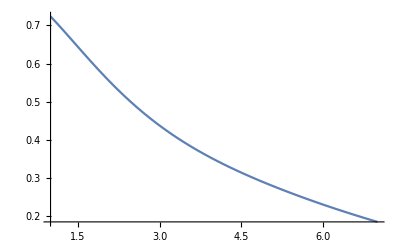

```mathematica
TopoSusceptibility[L_, β_] := (
d = L^2;
x = β/2;

term = (BesselI[Abs[q], 2 Sqrt[x^2 - y^2]] ((x-y)/(x+y))^(q/2))^d;
Dterm = D[term, y]/.{y-> 0};
DDterm = D[term, {y, 2}]/.{y-> 0};
term = term/.{y-> 0};
term0 = term/.{q -> 0};
cut = 3;
Z = NSum[term/term0, {q, -cut, cut}];
DZ = NSum[Dterm/term0, {q, -cut, cut}];
DDZ = NSum[DDterm/term0, {q, -cut, cut}];

chi = - (1/(4 π)^2) ((DDZ/Z) - (DZ/Z)^2)
)



TopoSusceptibility[8, 2.0]

Plot[TopoSusceptibility[8, β], {β, 1, 7}]
```